```mathematica
ClearAll[cp,xgv,t,kka,i]
SetDirectory[NotebookDirectory[]];
f=1;(*bioaviability*)
dose=400; (*standard doses*)
dis=61; (*Discriminant between male and female on VD*)
(*Import parameters from data analysis*)
parameters=Import["personal-parameters.txt","Table"];
(*      parameters[[1]]=beta
     parameters[[2]]=sex
    parameters[[3]]=age
   parameters[[4]]=weight  
  parameters[[5]]=k_a
 parameters[[6]]=CL
parameters[[7]]=V  *)
npat=Length[parameters];

cl=Table[0,{npat}];
ka=Table[0,{npat}];
v=Table[0,{npat}];
beta=Table[0,{npat}];

For[i=1,i<=npat,i++,{
cl[[i]]=parameters [[i]][[6]],
ka[[i]]=parameters [[i]][[5]],
v[[i]]=parameters [[i]][[7]]-(1-parameters [[i]][[2]])*dis+dis*parameters [[i]][[2]],
beta[[i]]=parameters [[i]][[1]]
}]

ndose=4;
avg=Table[0,{npat}]; (*average patient conc*)
n1=Table[0,{npat}]; (*average patient eff*)
n2=Table[0,{npat}]; (*average patient eff*)
di=Table[0,{npat}]; (*result*)
dis=Table[0,{npat}]; (*result*)
kk=1/0.377;
tmax=ndose*24;(*ore di terapia*)
p1=0.45;
a1=0.87;
Emax=1;
E50=0.1234;
vdosi=Table[dose,{ndose}]; (*array of doses*)
xgv=Table [0,{ndose}]; (*GI concentration*)


(*Multidose GI concentration*)
(*Loop over patients*)
For[ii=1,ii<=npat,ii++,{

xgv[[1]]=f*vdosi[[1]]*Exp[-ka[[ii]]*t];

For[i=2,i≤ndose,i++,{

xgv[[i]]=xgv[[i-1]]+UnitStep[t-24*(i-1)]*f*vdosi[[i]]*Exp[-ka[[ii]]*(t-(i-1)*24)]

}],



ClearAll[t],
eqsc=Join[{D[cp[t],t]==-cl[[ii]]*cp[t]/v[[ii]]+ka[[ii]]*xgv[[ndose]],cp[0]==0}],
solc=NDSolve[eqsc,cp[t],{t,0,tmax}],
avg[[ii]]=Simplify[(NIntegrate[Evaluate[cp[t]/.solc]/v[[ii]],{t,48,tmax}][[1]])/(tmax-48)],
di[[ii]]=((2*a1-1)*p1-(beta[[ii]])/Log10[N[E]]),
n2[[ii]]=(Emax*avg[[ii]]-(kk)*di[[ii]]*avg[[ii]])/((kk)*di[[ii]])
}](* end of patients loop*)
```

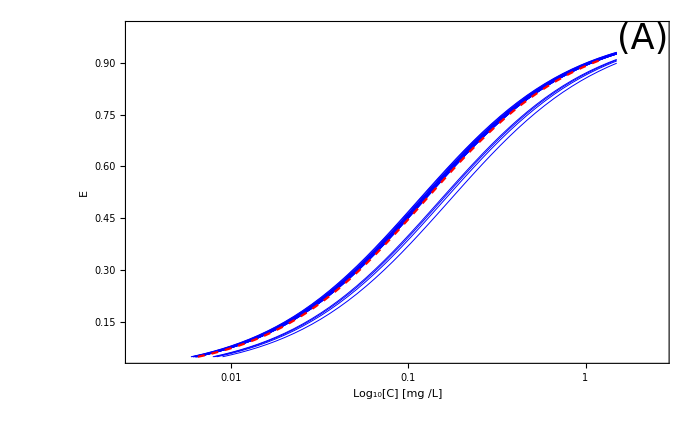

```mathematica
a1=LogLinearPlot[((Emax*c))/(n2[[1]]+c),{c,0.005,1.5},PlotRange->{0.05,1},FrameTicks->{{Automatic,Automatic},{{0.005,0.01,0.05,0.1,0.5,1},Automatic}},FrameLabel->{Row[{Subscript["Log","10"],,"[","C","]"," [","mg "," /","L","]"}],"E"},PlotStyle->{{Blue,Automatic,Thickness[0.001]}},Frame->True,PlotStyle->Thickness[0.001],FrameStyle->Thickness[0.005],FrameTicksStyle->{{FontSize->35,FontSize->35},{FontSize->35,FontSize->35}},LabelStyle->Directive[Black,45],PlotStyle->{Blue},GridLines->{Automatic,Automatic},Axes->False,GridLinesStyle->Black];
a2=LogLinearPlot[((Emax*c))/(n2[[2]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a3=LogLinearPlot[((Emax*c))/(n2[[3]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a4=LogLinearPlot[((Emax*c))/(n2[[4]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a5=LogLinearPlot[((Emax*c))/(n2[[5]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a6=LogLinearPlot[((Emax*c))/(n2[[6]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a7=LogLinearPlot[((Emax*c))/(n2[[7]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a8=LogLinearPlot[((Emax*c))/(n2[[8]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a9=LogLinearPlot[((Emax*c))/(n2[[9]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a10=LogLinearPlot[((Emax*c))/(n2[[10]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a11=LogLinearPlot[((Emax*c))/(n2[[11]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a12=LogLinearPlot[((Emax*c))/(n2[[12]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a13=LogLinearPlot[((Emax*c))/(n2[[13]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a14=LogLinearPlot[((Emax*c))/(n2[[14]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a15=LogLinearPlot[((Emax*c))/(n2[[15]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a16=LogLinearPlot[((Emax*c))/(n2[[16]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a17=LogLinearPlot[((Emax*c))/(n2[[17]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a18=LogLinearPlot[((Emax*c))/(n2[[18]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a19=LogLinearPlot[((Emax*c))/(n2[[19]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a20=LogLinearPlot[((Emax*c))/(n2[[20]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a21=LogLinearPlot[((Emax*c))/(n2[[21]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a22=LogLinearPlot[((Emax*c))/(n2[[22]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
ast=LogLinearPlot[((Emax*c))/(0.1234+c),{c,0.005,1.2},PlotRange->{0.05,1},PlotStyle->{Red,Dashed},GridLines->{None,None}];
normal=Show[a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12,a13,a14,a15,a16,a17,a18,a19,a20,a21,a22,ast,Epilog->{Inset[Style["(A)     ",35],Offset[{-1,-1},Scaled[{1,1}]],{Right,Top}],Inset[Framed[Column[{LineLegend[{Red,Dashed},{"Average"},LabelStyle->35],LineLegend[{Blue},{"Single patients"},LabelStyle->35]}],RoundingRadius->5],Scaled[{0,0.9}],{-1.1,0.10}]}]



(*a1=LogLinearPlot[((Emax*c))/(n2[[1]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},FrameLabel->{Row[{Subscript["Log","10"],,"[","C","]"," [","mg "," /","L","]"}],"E"},PlotStyle->{{Blue,Automatic,Thickness[0.001]}},Frame->True,PlotStyle->Thickness[0.001],FrameStyle->Thickness[0.005],FrameTicksStyle->{{FontSize->25,FontSize->25},{FontSize->25,FontSize->25}},LabelStyle->Directive[Black,35],PlotStyle->{Blue},GridLines->{None,None},Axes->False];
a2=LogLinearPlot[((Emax*c))/(n2[[2]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a3=LogLinearPlot[((Emax*c))/(n2[[3]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a4=LogLinearPlot[((Emax*c))/(n2[[4]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a5=LogLinearPlot[((Emax*c))/(n2[[5]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a6=LogLinearPlot[((Emax*c))/(n2[[6]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a7=LogLinearPlot[((Emax*c))/(n2[[7]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a8=LogLinearPlot[((Emax*c))/(n2[[8]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a9=LogLinearPlot[((Emax*c))/(n2[[9]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a10=LogLinearPlot[((Emax*c))/(n2[[10]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a11=LogLinearPlot[((Emax*c))/(n2[[11]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a12=LogLinearPlot[((Emax*c))/(n2[[12]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a13=LogLinearPlot[((Emax*c))/(n2[[13]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a14=LogLinearPlot[((Emax*c))/(n2[[14]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a15=LogLinearPlot[((Emax*c))/(n2[[15]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a16=LogLinearPlot[((Emax*c))/(n2[[16]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a17=LogLinearPlot[((Emax*c))/(n2[[17]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a18=LogLinearPlot[((Emax*c))/(n2[[18]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a19=LogLinearPlot[((Emax*c))/(n2[[19]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a20=LogLinearPlot[((Emax*c))/(n2[[20]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a21=LogLinearPlot[((Emax*c))/(n2[[21]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a22=LogLinearPlot[((Emax*c))/(n2[[22]]+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
ast=LogLinearPlot[((Emax*c))/(0.1234+c),{c,0.6,0.7},PlotRange->{0.75,0.87},PlotStyle->{Red,Dashed,Thickness[0.001]},GridLines->{None,None}];
zoom=Show[a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12,a13,a14,a15,a16,a17,a18,a19,a20,a21,a22,ast,Epilog->Inset[Framed[Column[{LineLegend[{Directive[Red,Dashed,36]},{"Average",36}],LineLegend[{Directive[Blue,36]},{"Single patients",36}],36}],RoundingRadius->5],Scaled[{8.0,10}],{9,0.9}]]*)
```

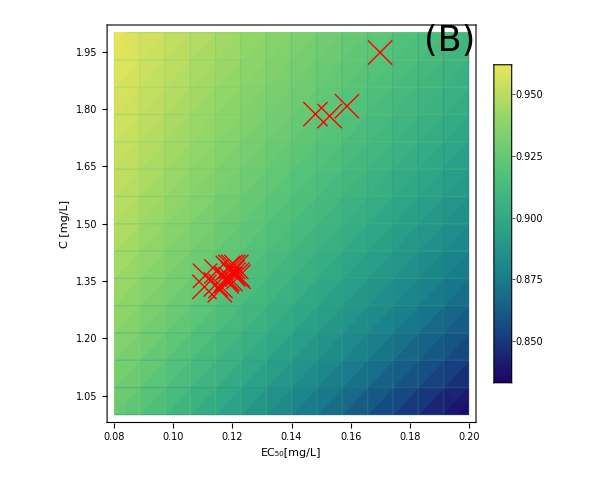

```mathematica
al=Plot3D[(c)/(e50+c),{e50,0.01,0.2},{c,1,2},AxesLabel->{Row[{Subscript["EC","50"],"[","m","g"," /","L","]"}],Row[{"C","[","m","g ","/","L","]"}],"E"},ColorFunction->"BlueGreenYellow",LabelStyle->Directive[Medium]];
dnes=DensityPlot[(c)/(e50+c),{e50,0.08,0.2},{c,1,2},ColorFunction->"BlueGreenYellow",LabelStyle->{None},FrameTicks->Automatic,FrameLabel->{Row[{Subscript["EC","50"],"[","m","g","/","L","]"}],Row[{OverBar["C"]," [","m","g","/","L","]"}]},LabelStyle->Directive[25,Bold],PlotLegends->BarLegend[Automatic,LegendLabel->None],Mesh->Full,FrameTicksStyle->{{None,None},{None,None}},AxesLabel->{False,False}];

cmed={1.3871014576650726,1.3553857589804656,1.3259792420523837,1.3496907094221782,1.366880430703683,1.384126027756881,1.3370483444822931,1.8076164912121389,1.7868919525226652,1.3348210558312572,1.3640108326716915,1.7817802339848403,1.3412294883213411,1.3610973019952177,1.3553857589804656,1.3553857589804656,1.366908076374406,1.3871014576650726,1.3752689112974954,1.3871014576650726,1.9480213677953402,1.372708426769277};
e50dat={0.12131092883934216,0.11828415064546921,0.11572954839871628,0.11801862858141134,0.12167188087970633,0.11846104485641944,0.11596346245054313,0.15873786930341466,0.14808658245047096,0.11052102298338941,0.11073359262960873,0.15289758183335753,0.11439710952950977,0.12203502873390251,0.11798329373068482,0.11935627618748139,0.12037184282069137,0.11933868441164311,0.1145858760636967,0.12028009677395876,0.16995635012120586,0.11995682323379692};
points=Table[0,{Length[e50dat]}];
points2d=Table[0,{Length[e50dat]}];


For[i=1,i≤Length[e50dat],i++,{points[[i]]={e50dat[[i]],cmed[[i]],(cmed[[i]])/(e50dat[[i]]+cmed[[i]])},points2d[[i]]={e50dat[[i]],cmed[[i]]}}]
ai=ListPointPlot3D[points,FillingStyle->Directive[Red,Thick,Opacity[.5]],PlotStyle->{PointSize[0.08]}];
a2d=ListPlot[points2d,PlotStyle->{Red},PlotMarkers->{"×",25}];
ll=Show[al,ai];
llll=Show[dnes,a2d,Epilog->Inset[Style["(B)     ",35],Offset[{-1,1},Scaled[{1,1}]],{Right,Top}],ImageSize->500]
GraphicsRow[{ll,llll}];
```

```mathematica
(*a1=LogLinearPlot[((Emax*c))/(n2[[1]]+c),{c,0.005,1.5},PlotRange->{0.05,1},FrameTicks->{{Automatic,Automatic},{{0.005,0.01,0.05,0.1,0.5,1},Automatic}},PlotStyle->{{Blue,Automatic,Thickness[0.001]}},Frame->True,PlotStyle->Thickness[0.001],FrameStyle->Thickness[0.005],FrameTicksStyle->{{FontSize->0,FontSize->0},{FontSize->0,FontSize->0}},LabelStyle->Directive[Black,45],PlotStyle->{Blue},GridLines->{Automatic,Automatic},Axes->False,GridLinesStyle->Black];
a2=LogLinearPlot[((Emax*c))/(n2[[2]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a3=LogLinearPlot[((Emax*c))/(n2[[3]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a4=LogLinearPlot[((Emax*c))/(n2[[4]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a5=LogLinearPlot[((Emax*c))/(n2[[5]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a6=LogLinearPlot[((Emax*c))/(n2[[6]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a7=LogLinearPlot[((Emax*c))/(n2[[7]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a8=LogLinearPlot[((Emax*c))/(n2[[8]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{RGBColor[1,0,1],Thickness[0.001]},GridLines->{None,None}];
a9=LogLinearPlot[((Emax*c))/(n2[[9]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{RGBColor[1,0,1],Thickness[0.001]},GridLines->{None,None}];
a10=LogLinearPlot[((Emax*c))/(n2[[10]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a11=LogLinearPlot[((Emax*c))/(n2[[11]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a12=LogLinearPlot[((Emax*c))/(n2[[12]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a13=LogLinearPlot[((Emax*c))/(n2[[13]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a14=LogLinearPlot[((Emax*c))/(n2[[14]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a15=LogLinearPlot[((Emax*c))/(n2[[15]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{RGBColor[1,0,0.2],Thickness[0.001]},GridLines->{None,None}];
a16=LogLinearPlot[((Emax*c))/(n2[[16]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a17=LogLinearPlot[((Emax*c))/(n2[[17]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a18=LogLinearPlot[((Emax*c))/(n2[[18]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a19=LogLinearPlot[((Emax*c))/(n2[[19]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a20=LogLinearPlot[((Emax*c))/(n2[[20]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
a21=LogLinearPlot[((Emax*c))/(n2[[21]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{RGBColor[1,0,1],Thickness[0.001]},GridLines->{None,None}];
a22=LogLinearPlot[((Emax*c))/(n2[[22]]+c),{c,0.005,1.5},PlotRange->{0.05,1},PlotStyle->{Blue,Thickness[0.001]},GridLines->{None,None}];
ast=LogLinearPlot[((Emax*c))/(0.1234+c),{c,0.005,1.2},PlotRange->{0.05,1},PlotStyle->{Red,Dashed},GridLines->{None,None}];
normal=Show[a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12,a13,a14,a15,a16,a17,a18,a19,a20,a21,a22,ast]*)
```

```mathematica
(*al=Plot3D[(c)/(e50+c),{e50,0.01,0.2},{c,1,2},AxesLabel->{Row[{Subscript["EC","50"],"[","m","g"," /","L","]"}],Row[{"C","[","m","g ","/","L","]"}],"E"},ColorFunction->"BlueGreenYellow",LabelStyle->Directive[Medium]]
dnes=DensityPlot[(c)/(e50+c),{e50,0.01,0.2},{c,1,2},ColorFunction->"BlueGreenYellow",FrameLabel->{Row[{Subscript["EC","50"],"[","m","g","/","L","]"}],Row[{OverBar["C"]," [","m","g","/","L","]"}]},LabelStyle->Directive[25,Bold],PlotLegends->BarLegend[Automatic,LegendLabel->"E"],Mesh->Full,FrameTicksStyle->{{FontSize->25,FontSize->25},{FontSize->25,FontSize->25}}];

cmed={1.3871014576650726,1.3553857589804656,1.3259792420523837,1.3496907094221782,1.366880430703683,1.384126027756881,1.3370483444822931,1.8076164912121389,1.7868919525226652,1.3348210558312572,1.3640108326716915,1.7817802339848403,1.3412294883213411,1.3610973019952177,1.3553857589804656,1.3553857589804656,1.366908076374406,1.3871014576650726,1.3752689112974954,1.3871014576650726,1.9480213677953402,1.372708426769277};
e50dat={0.12131092883934216,0.11828415064546921,0.11572954839871628,0.11801862858141134,0.12167188087970633,0.11846104485641944,0.11596346245054313,0.15873786930341466,0.14808658245047096,0.11052102298338941,0.11073359262960873,0.15289758183335753,0.11439710952950977,0.12203502873390251,0.11798329373068482,0.11935627618748139,0.12037184282069137,0.11933868441164311,0.1145858760636967,0.12028009677395876,0.16995635012120586,0.11995682323379692};
points=Table[0,{Length[e50dat]}];
points2d=Table[0,{Length[e50dat]}];


For[i=1,i≤Length[e50dat],i++,{points[[i]]={e50dat[[i]],cmed[[i]],(cmed[[i]])/(e50dat[[i]]+cmed[[i]])},points2d[[i]]={e50dat[[i]],cmed[[i]]}}]
ai=ListPointPlot3D[points,FillingStyle->Directive[Red,Thick,Opacity[.5]]];
a2d=ListPlot[points2d,PlotStyle->Red,PlotMarkers->"▼"];
ll=Show[al,ai]
llll=Show[dnes,a2d,Epilog->Inset[Style["(B)     ",35],Offset[{-1,1},Scaled[{1,1}]],{Right,Top}]];
GraphicsRow[{ll,llll}]
```

```mathematica
(*dnes=DensityPlot[(c)/(e50+c),{e50,0.01,0.2},{c,1,2},ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[Automatic],Mesh->Full,FrameTicksStyle->{{FontSize->0,FontSize->0},{FontSize->0,FontSize->0}}];

For[i=1,i≤Length[e50dat],i++,{points[[i]]={e50dat[[i]],cmed[[i]],(cmed[[i]])/(e50dat[[i]]+cmed[[i]])},points2d[[i]]={e50dat[[i]],cmed[[i]]}}]
ai=ListPointPlot3D[points,FillingStyle->Directive[Red,Thick,Opacity[.5]]];
a2d=ListPlot[points2d,PlotStyle->Red,PlotMarkers->"▼",FrameTicksStyle->{{FontSize->0,FontSize->0},{FontSize->0,FontSize->0}}];
llll=Show[dnes,a2d]*)
```